```mathematica
A[a0_,  aUV_, aIR_, x_]:= a0 + (aUV*x^2)/(x^2-0.1066^2)+(aIR*x^2)/(x^2-0.9083^2);
n[a0_,  aUV_, aIR_, x_] := √(1+(3*A[a0, aUV, aIR,x])/(3-A[a0, aUV, aIR,x]))
```

```mathematica
D[n[a0, aUV, aIR,x], x] /. {a0-> 0.335, aUV-> 0.099, aIR-> 0.008,x-> 0.128}
```

-6.90687

```mathematica
-6.906873929232762
```

-6.90687

```mathematica
D[n[a0, aUV, aIR,x], x]
```

((3 (-(2 aIR x^3)/((-0.825009+x^2)^2)+(2 aIR x)/(-0.825009+x^2)-(2 aUV x^3)/((-0.0113636+x^2)^2)+(2 aUV x)/(-0.0113636+x^2)))/(3-a0-(aIR x^2)/(-0.825009+x^2)-(aUV x^2)/(-0.0113636+x^2))-(3 ((2 aIR x^3)/((-0.825009+x^2)^2)-(2 aIR x)/(-0.825009+x^2)+(2 aUV x^3)/((-0.0113636+x^2)^2)-(2 aUV x)/(-0.0113636+x^2)) (a0+(aIR x^2)/(-0.825009+x^2)+(aUV x^2)/(-0.0113636+x^2)))/(3-a0-(aIR x^2)/(-0.825009+x^2)-(aUV x^2)/(-0.0113636+x^2))^2)/(2 √(1+(3 (a0+(aIR x^2)/(-0.825009+x^2)+(aUV x^2)/(-0.0113636+x^2)))/(3-a0-(aIR x^2)/(-0.825009+x^2)-(aUV x^2)/(-0.0113636+x^2))))

```mathematica
D[n[a0, aUV, aIR,x], x] /. {x-> 0.1268}
```

((3 (-0.319731 aIR-129.646 aUV))/(3-a0+0.0198759 aIR-3.41025 aUV)-(3 (a0-0.0198759 aIR+3.41025 aUV) (0.319731 aIR+129.646 aUV))/(3-a0+0.0198759 aIR-3.41025 aUV)^2)/(2 √(1+(3 (a0-0.0198759 aIR+3.41025 aUV))/(3-a0+0.0198759 aIR-3.41025 aUV)))

```mathematica
((3 (-0.3197314047064091 aIR-129.64602816888623 aUV))/(3-a0+0.01987591890602736 aIR-3.4102505366217852 aUV)-(3 (a0-0.01987591890602736 aIR+3.4102505366217852 aUV) (0.3197314047064091 aIR+129.64602816888623 aUV))/(3-a0+0.01987591890602736 aIR-3.4102505366217852 aUV)^2)/(2 √(1+(3 (a0-0.01987591890602736 aIR+3.4102505366217852 aUV))/(3-a0+0.01987591890602736 aIR-3.4102505366217852 aUV)))
```

```mathematica
(3 (-0.3230013842555586 aIR-115.41727394429614 aUV))/(3-a0+0.020261557865229696 aIR-3.2634589796910234 aUV)/.{a0-> 0.335, aUV-> 0.099, aIR-> 0.008,x-> 0.128}
```

-14.6394

```mathematica
(3 (a0-0.020261557865229696 aIR+3.2634589796910234 aUV) (0.3230013842555586 aIR+115.41727394429614 aUV))/(3-a0+0.020261557865229696 aIR-3.2634589796910234 aUV)^2/.{a0-> 0.335, aUV-> 0.099, aIR-> 0.008,x-> 0.128}
```

4.1124

```mathematica
2 √(1+(3 (a0-0.020261557865229696 aIR+3.2634589796910234 aUV))/(3-a0+0.020261557865229696 aIR-3.2634589796910234 aUV))/.{a0-> 0.335, aUV-> 0.099, aIR-> 0.008,x-> 0.128}
```

2.71495

```mathematica
((3 (-0.3230013842555586 aIR-115.41727394429614 aUV))/(3-a0+0.020261557865229696 aIR-3.2634589796910234 aUV)-(3 (a0-0.020261557865229696 aIR+3.2634589796910234 aUV) (0.3230013842555586 aIR+115.41727394429614 aUV))/(3-a0+0.020261557865229696 aIR-3.2634589796910234 aUV)^2)/(2 √(1+(3 (a0-0.020261557865229696 aIR+3.2634589796910234 aUV))/(3-a0+0.020261557865229696 aIR-3.2634589796910234 aUV)))/.{a0-> 0.335, aUV-> 0.099, aIR-> 0.008,x-> 0.128}
```

-6.90687

```mathematica
7.46*0.3 -6.906873929232761*0.128
```

1.35392

```mathematica
7.46*0.3
```

2.238

```mathematica
B[a0_,  a1_, a2_, x_]:= 1.2055*10^-2*2/3*34.49/(44.66*10^-3)*(a0/(91.012-x^-2)+a1/(89.892-x^-2)+a2/(214.02-x^-2));
n1[a0_,  a1_, a2_, x_]:= √(3/(1-B[a0, a1, a2,x])-2);
```

```mathematica
D[n1[a0, a1, a2,x], x]/.{x-> 0.128}
```

(9.57976 (-1.06128 a0-1.14526 a1-0.0407477 a2))/(√(-2+3/(1-6.3865 (0.0333591 a0+0.0346538 a1+0.0065366 a2))) (1-6.3865 (0.0333591 a0+0.0346538 a1+0.0065366 a2))^2)

```mathematica
n1[a0, a1, a2,x]/.{a0->0.2075 , a1-> 0.0415, a2-> 4.333,x-> 0.128}
```

1.38487

```mathematica
n1[a0, a1, a2,x]/.{a0->0.1994, a1-> 0.0431, a2-> 4.299,x-> 0.128}
```

1.37972

```mathematica
D[n1[a0, a1, a2,x], x]/.{a0->0.2075 , a1-> 0.0415, a2-> 0.4333,x-> 0.128}
```

```mathematica
(3 (-0.3197314047064091 aIR-129.64602816888623 aUV))/(3-a0+0.01987591890602736 aIR-3.4102505366217852 aUV)
```

```mathematica
(3 (a0-0.01987591890602736 aIR+3.4102505366217852 aUV) (0.3197314047064091 aIR+129.64602816888623 aUV))/(3-a0+0.01987591890602736 aIR-3.4102505366217852 aUV)^2
```

```mathematica
2 √(1+(3 (a0-0.01987591890602736 aIR+3.4102505366217852 aUV))/(3-a0+0.01987591890602736 aIR-3.4102505366217852 aUV))
```

```mathematica
n1[a0, a1, a2,x]/.{a0->0.1994, a1-> 0.0431, a2-> 4.299,x-> 0.128}
```

1.36777

```mathematica
n[a0, aUV, aIR,x]/.{a0-> 0.335, aUV-> 0.0987, aIR-> 0.00804, x-> 0.128}
n[a0, aUV, aIR,x]/.{a0-> 0.335-0.0018, aUV-> 0.0987-0.0008, aIR-> 0.00804-0.0029, x-> 0.128}
n[a0, aUV, aIR,x]/.{a0-> 0.335+0.0018, aUV-> 0.0987+0.0008, aIR-> 0.00804+0.0029, x-> 0.128}
```

1.35688

1.35426

1.35951

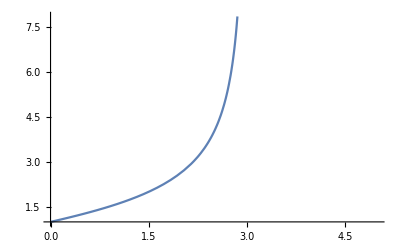

```mathematica
y[x_]:= √(1+(3*x)/(3-x));
Plot[y[x], {x, 0, 5}]
```

```mathematica
A[a0,  aUV, aIR, x]/.{a0-> 0.335, aUV-> 0.0987, aIR-> 0.00804, x-> 0.128}
```

```mathematica
0.6569404983702676
```

0.65694

0.604093

```mathematica
(*计算用Babizc模型得到的折射率误差*)
```

```mathematica
CovBA = {{3.455*10^-6,-9.443*10^-7,4.168*10^-6}, {-9.443*10^-7,6.845*10^-7,-3.854*10^-7}, {4.168*10^-6,-3.854*10^-7,8.4044*10^-6}}
```

{{3.455×10^-6,-9.443×10^-7,4.168×10^-6},{-9.443×10^-7,6.845×10^-7,-3.854×10^-7},{4.168×10^-6,-3.854×10^-7,8.4044×10^-6}}

```mathematica
D[n[a0, aUV, aIR, x], aIR] /.{a0-> 0.335, aUV-> 0.0987, aIR-> 0.00804, x-> 0.128}
```

-0.0122399

```mathematica
v = {0.6040925185485628, 1.9714311542214735, -0.012239855520524052 }
```

{0.604093,1.97143,-0.0122399}

```mathematica
vT = {{0.6040925185485628}, {1.9714311542214735}, {-0.012239855520524052}}
```

{{0.604093},{1.97143},{-0.0122399}}

```mathematica
√(v.CovBA.vT)
```

{0.00127679}

```mathematica
(*计算用Zhou模型，不加群速度约束得到的折射率误差*)
```

```mathematica
CovZhou = {{2.549*10^-3,-1.290*10^-3,-3.008*10^-3}, {-1.290*10^-3,2.484*10^-3,-2.969*10^-3}, {-3.008*10^-3, -2.969*10^-3,1.463*10^-2}};
```

```mathematica
D[n1[a0, a1, a2,x], a2]/.{a0->0.2073 , a1-> 0.0742, a2-> 4.215,x-> 0.128}
```

0.0745273

```mathematica
0.07734224869289487
n1[a0, a1, a2,x]/.{a0->0.2073 , a1-> 0.0742, a2-> 4.215,x-> 0.128}
```

0.0773422

1.37677

```mathematica
v1 = {0.3803451466170621, 0.39510721026829254,0.0745272979449019};
v1T = {{0.3803451466170621}, {0.39510721026829254}, {0.0745272979449019}};
√(v1.CovZhou.v1T)
```

{0.0102315}

```mathematica
(*计算用Zhou模型，加群速度约束得到的折射率误差*)
```

```mathematica
CovZhouGV = {{1.253*10^-3,-1.147*10^-3,-2.211*10^-4},{-1.147*10^-3,1.073*10^-3,1.432*10^-4}, {-2.211*10^-4,1.432*10^-4,2.682*10^-4}}
```

{{0.001253,-0.001147,-0.0002211},{-0.001147,0.001073,0.0001432},{-0.0002211,0.0001432,0.0002682}}

```mathematica
D[n1[a0, a1, a2,x], a2]/.{a0->0.3452 , a1-> 0.0190, a2-> 4.0160,x-> 0.128}
```

0.0753513

```mathematica
v2 = {0.3845502165740034, 0.39947548859246124, 0.07535126665949587}
v2T = {{0.3845502165740034}, {0.39947548859246124}, {0.07535126665949587}}
√(v2.CovZhouGV.v2T)
```

{0.38455,0.399475,0.0753513}

{{0.38455},{0.399475},{0.0753513}}

{0.00120502}

```mathematica
n1[a0, a1, a2,x]/.{a0->0.345227, a1-> 0.0189568, a2-> 4.01598,x-> 0.128}
```

1.39266

```mathematica
(*Rayleigh scattering length*)
kT = 2.18*10^-9;
kB = 1.380649*10^-23   ; 
T = 90;
f = 10^22;
Lray[y_]:= 1/((8*Pi^3)/(3*0.128^4)*(((y*y-1)*(y*y+2))/3)^2*kB*kT*T *f)
```

```mathematica
n[a0, aUV, aIR, x]/.{a0-> 0.335, aUV-> 0.099, aIR-> 0.008, x->0.128}
```

```mathematica
1.3574751001515895
```

1.35748

```mathematica
Lray[1.3574751001515895]
```

102.852

```mathematica
Lray[1.3564751001515895]
```

103.664

```mathematica
Lray[1.3584751001515895]
```

102.048

```mathematica
n[a0, aUV, aIR, x]/.{a0-> 0.335, aUV-> 0.0987, aIR-> 0.00803, x->0.128}
```

1.35688

```mathematica
Lray[1.3568831851298473]
```

103.332

```mathematica
Lray[1.356883185129847-0.00127679]
```

104.376

```mathematica
Lray[1.356883185129847+0.00127679]
```

102.301

```mathematica
n1[a0, a1, a2, x] /.{a0-> 0.207, a1-> 0.0742, a2-> 4.2148, x->0.128}
```

1.37664

```mathematica
Lray[1.3766428478683999]
```

```mathematica
88.72521897733415
Lray[1.3766428478683999-0.0102315]
Lray[1.3766428478683999+0.0102315]
```

88.7252

95.9394

82.1775

```mathematica
n1[a0, a1, a2, x] /.{a0-> 0.3452, a1-> 0.0190, a2-> 4.0160, x->0.128}
```

1.39267

```mathematica
Lray[1.3926674847221425]
Lray[1.3926674847221425-0.00120502]
Lray[1.3926674847221425+0.00120502]
```

78.7372

79.4378

78.0443

```mathematica
kT90 = kT*102.852/99.9
```

2.24442×10^-9